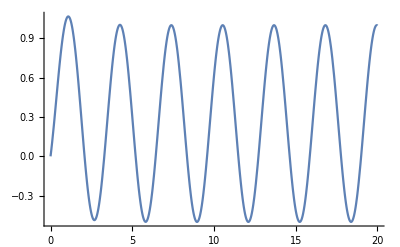

```mathematica
Plot[-0.45Cos[2t]+0.6Sin[2t]+0.25+0.2Exp[-t],{t,0,20}, PlotRange->All]
```

```mathematica
s=DSolve[{2x''[t]+x[t]==3Cos[0.7t],x[0]==1,x'[0]==0}, x[t],t]
```

{{x[t]→149.246 (-0.99835 Cos[0.707107 t]+1. Cos[0.00710678 t] Cos[0.707107 t]+0.00505063 Cos[0.707107 t] Cos[1.40711 t]+1. Sin[0.00710678 t] Sin[0.707107 t]+0.00505063 Sin[0.707107 t] Sin[1.40711 t])}}

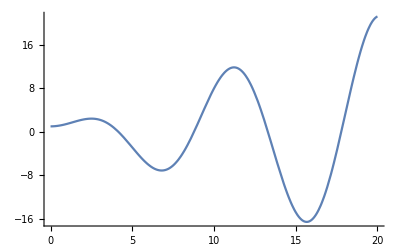

```mathematica
b=Plot[Evaluate[x[t]/. s],{t,0,20}, PlotRange->All]
```

```mathematica
Clear[x];
h=DSolve[{4x''[t]+9x[t]==Sin[1.5t], x[0]==1, x'[0]==0}, x[t], t]
```

{{x[t]→-0.0833333 (-12. Cos[1.5 t]+1. t Cos[1.5 t]-0.333333 Sin[1.5 t]+0.333333 Cos[3. t] Sin[1.5 t]-0.333333 Cos[1.5 t] Sin[3. t])}}

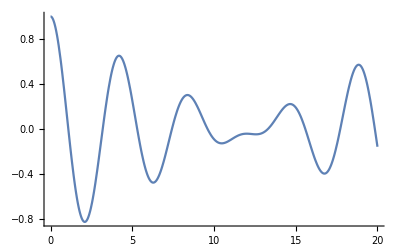

```mathematica
c=Plot[Evaluate[x[t] /. h], {t,0,20}, PlotRange->All]
```

```mathematica
j=DSolve[{x''[t]+x'[t]+2.732x[t]==Sin[t], x[0]==0, x'[0]==0}, x[t],t]
```

{{x[t]→-0.273066 ⅇ^(-0.5 t) (-0.915569 Cos[1.57544 t]+1. ⅇ^(0.5 t) Cos[0.575436 t] Cos[1.57544 t]-0.0844309 ⅇ^(0.5 t) Cos[1.57544 t] Cos[2.57544 t]+1.15087 ⅇ^(0.5 t) Cos[1.57544 t] Sin[0.575436 t]+(0.71598-6.45181×10^-17 ⅈ) Sin[1.57544 t]-(1.15087-6.45181×10^-17 ⅈ) ⅇ^(0.5 t) Cos[0.575436 t] Sin[1.57544 t]+0.434893 ⅇ^(0.5 t) Cos[2.57544 t] Sin[1.57544 t]+1. ⅇ^(0.5 t) Sin[0.575436 t] Sin[1.57544 t]-0.434893 ⅇ^(0.5 t) Cos[1.57544 t] Sin[2.57544 t]-0.0844309 ⅇ^(0.5 t) Sin[1.57544 t] Sin[2.57544 t])}}

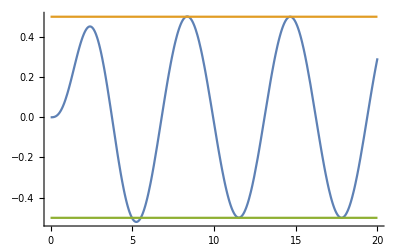

```mathematica
Plot[{Evaluate[x[t]/.j], 0.5, -0.5}, {t,0,20}, PlotRange->All]
```

```mathematica
c= DSolve[{4x''[t]+4x'[t]+3x[t]==Sin[0.5t], x'[0]==0, x[0]==0}, x[t], t]
```

{{x[t]→-0.301777 ⅇ^(-0.5 t) (-0.828427 Cos[0.707107 t]+1. ⅇ^(0.5 t) Cos[0.207107 t] Cos[0.707107 t]-0.171573 ⅇ^(0.5 t) Cos[0.707107 t] Cos[1.20711 t]+0.414214 ⅇ^(0.5 t) Cos[0.707107 t] Sin[0.207107 t]+1.95106×10^-16 Sin[0.707107 t]-0.414214 ⅇ^(0.5 t) Cos[0.207107 t] Sin[0.707107 t]+0.414214 ⅇ^(0.5 t) Cos[1.20711 t] Sin[0.707107 t]+1. ⅇ^(0.5 t) Sin[0.207107 t] Sin[0.707107 t]-0.414214 ⅇ^(0.5 t) Cos[0.707107 t] Sin[1.20711 t]-0.171573 ⅇ^(0.5 t) Sin[0.707107 t] Sin[1.20711 t])}}

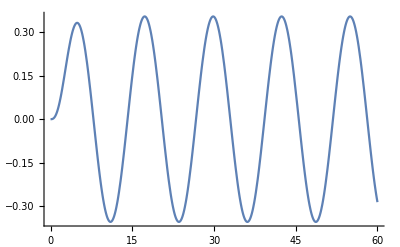

```mathematica
Plot[Evaluate[x[t]/.c], {t,0,60}, PlotRange->All]
```

```mathematica
k =DSolve[{4x''[t]+4x'[t]+3x[t]==Sin[0.25t], x'[0]==0, x[0]==0}, x[t], t]
```

{{x[t]→-0.19259 ⅇ^(-0.5 t) (-0.60641 Cos[0.707107 t]+1. ⅇ^(0.5 t) Cos[0.457107 t] Cos[0.707107 t]-0.39359 ⅇ^(0.5 t) Cos[0.707107 t] Cos[0.957107 t]+0.914214 ⅇ^(0.5 t) Cos[0.707107 t] Sin[0.457107 t]+0.160799 Sin[0.707107 t]-0.914214 ⅇ^(0.5 t) Cos[0.457107 t] Sin[0.707107 t]+0.753415 ⅇ^(0.5 t) Cos[0.957107 t] Sin[0.707107 t]+1. ⅇ^(0.5 t) Sin[0.457107 t] Sin[0.707107 t]-0.753415 ⅇ^(0.5 t) Cos[0.707107 t] Sin[0.957107 t]-0.39359 ⅇ^(0.5 t) Sin[0.707107 t] Sin[0.957107 t])}}

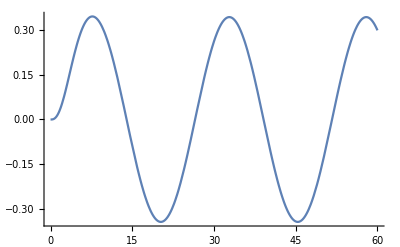

```mathematica
Plot[Evaluate[x[t]/.k], {t,0,60}, PlotRange->All]
```

```mathematica
ClearAll;
```

```mathematica
k1= 1;
k2=3;
v = 5;
```

{{y→InterpolatingFunction[…]}}

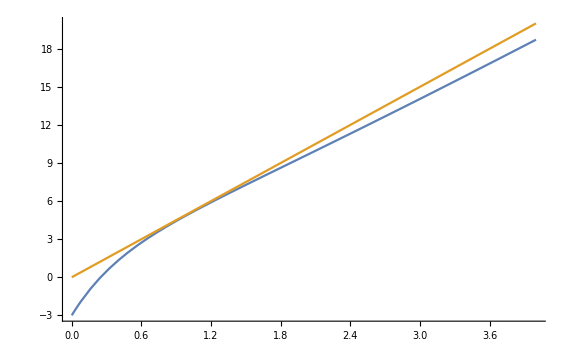

```mathematica
s=NDSolve[{y''[x]==k1(v x- y[x]-2)+k2(v-y'[x]),y[0]==-3,y'[0]==15},y,{x,0,5}]

Plot[{Evaluate[y[x]/.s],v x},{x,0,4},PlotRange->All]
```